## 今日の目標

直線や平面のベクトル方程式を理解し，幾何的なイメージをつかむ．

実行結果を保存したこのノートブックを授業後に提出してもらいます（PWP）．
その際，ファイル名の後半部分が学籍番号になるよう，x の部分を変更してください．

名　　前：
学籍番号：0xJKxxx

◀     |     ▶

## ベクトルの定義

ベクトル，点の座標は { } で表します．

```mathematica
a={1,2,3};
```

```mathematica
a
```

{1,2,3}

◀     |     ▶

## ベクトルの可視化（１）

ベクトル（矢印つき線分）は Arrow コマンドで可視化できます．

```mathematica
Graphics[Arrow[始点,終点}]]
```

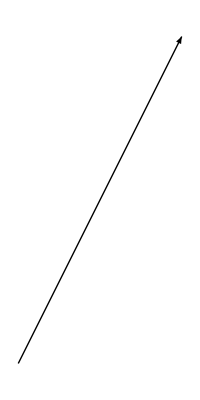

```mathematica
Graphics[Arrow[{{0,0},{1,2}}]]
```

◀     |     ▶

## ベクトルの可視化（２）

始点と方向でベクトルを与えるコマンド Vector を定義しましょう．

```mathematica
Vector[start_,direction_]:=Arrow[{start,start+direction}]
```

```mathematica
Vector[{1,3,2},{1,-2,1}]
```

Arrow[{{1,3,2},{2,1,3}}]

◀     |     ▶

## 線分の太さ，色を変える

ベクトルの線の太さや色を変えることができます

```mathematica
Graphics3D[{太さ (Thick),色,Vector[p,v]}]
```

```mathematica
p={1,2,3};
v={1,-1,2};
Graphics3D[{{Thick,Red,Vector[p,v]},{Thick,Blue,Vector[{0,0,0},v]}}]
```

-Graphics3D-

◀     |     ▶

## 課題

空間ベクトル a と b を適当に定めて，3つのベクトル a, b, a × b を描画しなさい（ベクトルの始点は原点とせよ）．
（外積はCross コマンドで計算できます）

```mathematica
Cross[{a,b,c},{x,y,z}]
```

```mathematica
p={1,2,3};
v1={1,-1,2};
v2={2,3,1};
Graphics3D[
{{Thick,Blue,Vector[p,v1]},
{Thick,Blue,Vector[p,v2]},
{Thick,Red,Vector[p,Cross[v1,v2]]}
}
]
```

-Graphics3D-

◀     |     ▶

## 直線のベクトル方程式（媒介変数表示）（１）

位置ベクトルp_0が表す点P_0を通り，v に平行な直線上の点（の位置ベクトル）p は

p = p_0 + t v

で表される（t は媒介変数）．

```mathematica
ParametricPlot[{x 座標 (tの関数),y 座標 (tの関数)},{t の動く範囲}]
```

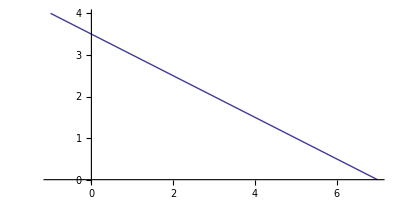

```mathematica
p0={3,2};
v={-2,1};
ParametricPlot[p0+t*v,{t,-2,2}]
```

◀     |     ▶

## 直線のベクトル方程式（媒介変数表示）（２）

位置ベクトルp_0と方向ベクトル v も描画してみよう（複数の図形を表示するには Show コマンドを用います）．

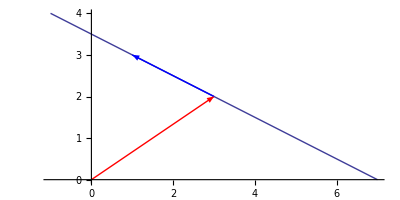

```mathematica
p0={3,2};
v={-2,1};
Show[
ParametricPlot[p0+t*v,{t,-2,2}],
Graphics[{Thick,Red,Vector[{0,0},p0]}],
Graphics[{Thick,Blue,Vector[p0,v]}]
]
```

◀     |     ▶

## 平面のベクトル方程式（１）

空間内の平面は，平面が通過する点（の位置ベクトル）p_0 と法線ベクトル n により定まる．この平面上の点 p は以下の関係式を満たす．

( p - p_0)・n = 0

```mathematica
ContourPlot3D[(x,y,z に関する式)==0,{x の範囲},{y の範囲},{z の範囲}]
```

```mathematica
p0={1,0,2};
n={1,1,1};
Show[
ContourPlot3D[({x,y,z}-p0).n==0,{x,-3,3},{y,-3,3},{z,-3,3}],
Graphics3D[{Thick,Red,Vector[{0,0,0},p0]}],
Graphics3D[{Thick,Blue,Vector[p0,n]}]
]
```

-Graphics3D-

◀     |     ▶

## 平面のベクトル方程式（２）

空間内の平面は，平面が通過する点（の位置ベクトル）p_0 と法線ベクトル n により定まる．この平面上の点 p は以下の関係式を満たす．

( p - p_0)・n = 0

p = (x, y, z) とおいて，x, y, z の方程式を求めてみよう（内積の計算は . （ピリオド））．

```mathematica
{a,b, c}.{x,y,z}
```

```mathematica
p0={1,0,2};
n={1,1,1};
({x,y,z}-p0).n==0
```

-3+x+y+z==0

◀     |     ▶

## 3点を通る平面のベクトル方程式（１）

空間内の3点 A(-1, 0, 2)，B(2,-2,1)，C(0, 2, -1) を通る平面の方程式を求めよう．

```mathematica
PA={-1,0,2};
PB={2,-2,1};
PC={0,2,-1};
Graphics3D[
{
{PointSize[Large],Point[{PA, PB, PC}]},
Text[A,PA+{0,0,0.2}],
Text[B,PB+{0,0,0.2}],
Text[C,PC+{0,0,0.2}]
}
]
```

-Graphics3D-

## 3点を通る平面のベクトル方程式（２）

空間内の3点 A(-1, 0, 2)，B(2,-2,1)，C(0, 2, -1) を通る平面の方程式を求めよう．

a = OverVector[CA] , b = OverVector[CB] のグラフィックスを追加せよ．

```mathematica
PA={-1,0,2};
PB={2,-2,1};
PC={0,2,-1};
Graphics3D[
{
{PointSize[Large],Point[{PA, PB, PC}]},
Text[A,PA+{0,0,0.2}],
Text[B,PB+{0,0,0.2}],
Text[C,PC+{0,0,0.2}],
{Thick,Blue,Arrow[{PC,PA}]},
{Thick,Blue,Arrow[{PC,PB}]}
}
]
```

-Graphics3D-

## 3点を通る平面のベクトル方程式（３）

空間内の3点 A(-1, 0, 2)，B(2,-2,1)，C(0, 2, -1) を通る平面の方程式を求めよう．

a × b のグラフィックスを追加せよ．

```mathematica
PA={-1,0,2};
PB={2,-2,1};
PC={0,2,-1};
va=PA-PC;
vb=PB-PC;
Graphics3D[
{
{PointSize[Large],Point[{PA, PB, PC}]},
Text[A,PA+{0,0,0.2}],
Text[B,PB+{0,0,0.2}],
Text[C,PC+{0,0,0.2}],
{Thick,Blue,Arrow[{PC,PA}]},
{Thick,Blue,Arrow[{PC,PB}]},
{Thick,Red,Vector[PC,Cross[va,vb]]}
}
]
```

-Graphics3D-

## 3点を通る平面のベクトル方程式（４）

空間内の3点 A(-1, 0, 2)，B(2,-2,1)，C(0, 2, -1) を通る平面の方程式を求めよう．

求める平面は，C を通り，a × b に直交する平面である．

```mathematica
PA={-1,0,2};
PB={2,-2,1};
PC={0,2,-1};
va=PA-PC;
vb=PB-PC;
Show[
ContourPlot3D[({x,y,z}-PC).Cross[va,vb]==0,{x,-8,8},{y,-8,8},{z,-8,8}],
Graphics3D[
{
{PointSize[Large],Point[{PA, PB, PC}]},
Text[A,PA+{0,0,0.2}],
Text[B,PB+{0,0,0.2}],
Text[C,PC+{0,0,0.2}],
{Thick,Blue,Arrow[{PC,PA}]},
{Thick,Blue,Arrow[{PC,PB}]},
{Thick,Red,Vector[PC,Cross[va,vb]]}
}
]
]
```

-Graphics3D-